```mathematica
PacletInstall["https://rulebasedintegration.org/Rubi-4.16.1.0.paclet"]
```

PacletObject[…]

```mathematica
First[PacletFind["Rubi"]]["Location"]
```

C:\Users\Asus\AppData\Roaming\Wolfram\Paclets\Repository\Rubi-4.16.1.0

```mathematica
<<Rubi`
```

```mathematica
f[x_]:=Sqrt[A/(D*x^2+F*x^2+g)]
f[x]
```

√(A/(g+D x^2+F x^2))

```mathematica
√(c/((g+D x^2+F x^2)^2))
```

√(c/((g+D x^2+F x^2)^2))

```mathematica
Steps[Int[f[x],x]]
```

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Int[1/(√(g+D x^2+F x^2)),x]

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Int[1/(√(g+(D+F) x^2)),x]

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Subst[Int[1/(1-(D+F) x^2),x],x,x/(√(g+(D+F) x^2))]

(√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) ArcTanh[(√(D+F) x)/(√(g+(D+F) x^2))])/(√(D+F))
Copy Steps

(√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) ArcTanh[(√(D+F) x)/(√(g+(D+F) x^2))])/(√(D+F))

```mathematica
g[x_]:=Sqrt[1 - (B^2-4*A*C)/(H*(A*x^2 + B*x+C))]
g[x]
```

√(1-(B^2-4 A C)/(H (C+B x+A x^2)))

```mathematica
Steps[Int[g[x],x]]
Integrate[g[x],x]
```

Int[√(1-(B^2-4 A C)/(H (C+B x+A x^2))),x]
Copy Steps

```mathematica
Integrate[√(1-F/(C+B x+A x^2)),x]//Simplify
```

(√((A (C+x (B+A x)))/(-B^2+4 A C)) √((C-F+x (B+A x))/(C+x (B+A x))) EllipticE[ArcSin[(√(A^2/(B^2-4 A C)) (B+2 A x))/A],(B^2-4 A C)/(B^2-4 A C+4 A F)])/(2 √(A^2/(B^2-4 A C)) √(-(A (C-F+x (B+A x)))/(B^2+4 A (-C+F))))

```mathematica
f[x_]:=((15*β)/(α*ϕ^2+β*x^2+γ*ϕ*x))[1-(ϕ^2/(48*β*((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)))[(σ-12γ)^2 - 4*(ϵ-12β)*(ν-12α)]] -3/2*(2*β*x+γ*ϕ)^2/((α*ϕ^2+β*x^2+γ*ϕ*x)^2)
f[x]
```

-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]

```mathematica
j[x_]:=((15*β*(β*x^2+(β+γ*ϕ)*x+(α+γ/2)*ϕ^2)^2)/(α*ϕ^2+β*x^2+γ*ϕ*x))[1-(ϕ^2/(48*β*((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)))[(σ-12γ)^2 - 4*(ϵ-12β)*(ν-12α)]] -3/2*(2*β*x+γ*ϕ)^2/((α*ϕ^2+β*x^2+γ*ϕ*x)^2)
j[x]
```

-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]

```mathematica
g[x_]:=((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)

g[x]

g1[x_]:=(α*ϕ^2+β*x^2+γ*ϕ*x)
g1[x]
```

x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2

x^2 β+x γ ϕ+α ϕ^2

```mathematica
d[x_]:= sqrt[B/g[x]]
d[x]//Simplify

d1[x_]:=sqrt[B/(g[x]*g1[x])]
d1[x]
```

sqrt[B/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)]

sqrt[B/((x^2 β+x γ ϕ+α ϕ^2) (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))]

```mathematica
Integrate[d[x],x]
```

∫sqrt[B/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)]ⅆx

```mathematica
f[x_]:=(1+1/g[x])^-(1)
f[x]
h[x_]:= 1+ A/(2*g[x])
h[x]
i[x_,A_]:= Sqrt[A/g[x]]
i[x,B]

i1[x_]:=Sqrt[A/(g[x]*g1[x])]
i1[x]
```

1/(1+1/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

1+(√(-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2) ϕ)/(2 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

√(B/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

√((√(-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2) ϕ)/((x^2 β+x γ ϕ+α ϕ^2) (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)))

```mathematica
j[x_]:=Integrate[i[x,-B],x]
j[x]
j1[x_]:=Integrate[i1[x],x]
j1[x]
```

-(2 √(B/(x^2 (12 β-ϵ)+x (12 γ-σ) ϕ+(12 α-ν) ϕ^2)) √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2) ArcTan[(x √(12 β-ϵ))/(√((-12 α+ν) ϕ^2)-√(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))])/(√(12 β-ϵ))

(2 √((x^2 β+x γ ϕ+α ϕ^2) (-12 x^2 β+x^2 ϵ-12 x γ ϕ+x σ ϕ-12 α ϕ^2+ν ϕ^2)) √((√(-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2) ϕ)/((x^2 β+x γ ϕ+α ϕ^2) (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))) (x-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β))^2 √(((-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (x-(-12 γ ϕ+σ ϕ-√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))/((x-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ-√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))) ((-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)-(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))) √(((-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (x-(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))/((x-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))) √(((x-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))/((x-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))) EllipticF[ArcSin[√(((x-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))/((x-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ)))))],(((-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)-(-12 γ ϕ+σ ϕ-√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))) ((-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)-(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))/(((-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)-(-12 γ ϕ+σ ϕ-√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))) ((-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)-(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))])/(√(-((x^2 β+x γ ϕ+α ϕ^2) (x^2 (12 β-ϵ)+12 α ϕ^2-ν ϕ^2+x (12 γ ϕ-σ ϕ)))) (-(-γ ϕ-√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)) (-(-γ ϕ+√(-4 α β ϕ^2+γ^2 ϕ^2))/(2 β)+(-12 γ ϕ+σ ϕ+√((12 γ ϕ-σ ϕ)^2-4 (12 β-ϵ) (12 α ϕ^2-ν ϕ^2)))/(2 (12 β-ϵ))))

```mathematica
l[x_]:=Integrate[h[x],x]
l[x]
```

x+(A ArcTanh[(24 x β-2 x ϵ+12 γ ϕ-σ ϕ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)

```mathematica
(-4*(ν-12α)*(ϵ-12β)+(σ-12γ)^2)//Expand
```

-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2

```mathematica
Series[i[x,A],{A,0,2}]
m[x_]:=Series[l[x],{x,0,2}]
m[x]
```

1-A/(2 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))-A^2/(8 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)^2)+O[A]^3

(A ArcTanh[(12 γ-σ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2))])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)+(1-A/(2 (12 α-ν) ϕ^2)) x+(A (12 γ-σ) x^2)/(4 (12 α-ν)^2 ϕ^3)+O[x]^3

```mathematica
k[x_,A_]:= A/(2*Sqrt[g[x]])+(12*β*Sqrt[g[x]])/A
k[x]
```

A/(2 √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))+(12 β √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))/A

```mathematica
l[x_,A_]:=Integrate[k[x,A],x]
l[x,A]
```

1/(2 A)(1/(12 β-ϵ)6 β (24 x β-2 x ϵ+12 γ ϕ-σ ϕ) √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)+1/(12 β-ϵ)^(3/2)(A^2 (12 β-ϵ)+3 β (144 γ^2+48 α (-12 β+ϵ)+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ^2) ArcTan[(24 x β-2 x ϵ+12 γ ϕ-σ ϕ)/(2 √(12 β-ϵ) √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))])

```mathematica
A = γ^2 - 4*β*α                      (*   ϕ^2*((σ-12*γ)^2-4*(ϵ-12*β)*(ν-12*α)) *)

V[φ_] := β*φ^2+γ*ϕ*φ+α*ϕ^2
V1[φ_]:=k*V[φ]
V[φ]
V1[φ]
```

-4 α β+γ^2

α ϕ^2+γ ϕ φ+β φ^2

k (α ϕ^2+γ ϕ φ+β φ^2)

```mathematica
g3[x_]:=- ((12*β)/V[x]-(ϕ^2*k(γ^2 - 4*α*β))/(4*β*V[x]^2)+(3*(2*β*x+γ*ϕ)^2)/(2*V[x]^2))
g3[x]
g3[x]//Together
```

(k (-4 α β+γ^2) ϕ^2)/(4 β (x^2 β+x γ ϕ+α ϕ^2)^2)-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)-(12 β)/(x^2 β+x γ ϕ+α ϕ^2)

(-72 x^2 β^3-72 x β^2 γ ϕ-4 k α β ϕ^2-48 α β^2 ϕ^2+k γ^2 ϕ^2-6 β γ^2 ϕ^2)/(4 β (x^2 β+x γ ϕ+α ϕ^2)^2)

```mathematica
g4[x_]:=(ϕ^2*x^2)/V[x]^2
g4[x]
```

(x^2 ϕ^2)/((x^2 β+x γ ϕ+α ϕ^2)^2)

```mathematica
x[y_]:=ϕ/(2*β)*(γ-Sqrt[4*α*β-γ^2]*Sinh[Sqrt[β]*y/(6*M)+C])
x[y]
```

(ϕ (γ-√(4 α β-γ^2) Sinh[C+(y √β)/(6 M)]))/(2 β)

```mathematica
g4[x[y]]//Expand//FullSimplify
```

(4 (γ^2-2 γ √(4 α β-γ^2) Sinh[C+(y √β)/(6 M)]+(4 α β-γ^2) Sinh[C+(y √β)/(6 M)]^2))/((4 α β+3 γ^2-4 γ √(4 α β-γ^2) Sinh[C+(y √β)/(6 M)]+(4 α β-γ^2) Sinh[C+(y √β)/(6 M)]^2)^2)

```mathematica
g5[x_]:=6/Sqrt[V[x]]
g5[x]
```

6/(√(x^2 β+x γ ϕ+α ϕ^2))

```mathematica
g6[x_]:=Steps[Int[g5[x],x]]
g6[x]
```

Dist[6,Int[1/(√(x^2 β+x γ ϕ+α ϕ^2)),x],x]

Dist[12,Subst[Int[1/(-x^2+4 β),x],x,(2 x β+γ ϕ)/(√(x^2 β+x γ ϕ+α ϕ^2))],x]

(6 ArcTanh[(2 x β+γ ϕ)/(2 √β √(x^2 β+x γ ϕ+α ϕ^2))])/(√β)
Copy Steps

(6 ArcTanh[(2 x β+γ ϕ)/(2 √β √(x^2 β+x γ ϕ+α ϕ^2))])/(√β)

-(6 Log[-2 x β-γ ϕ+2 √β √(x^2 β+x γ ϕ+α ϕ^2)])/(√β)

```mathematica
c = 10
r = 1
A = 1
```

10

1

1

```mathematica
v[x_]:= Tanh[A - Tanh[(x+r)/c]]
v[x]
```

Tanh[1-Tanh[(1+x)/1000]]

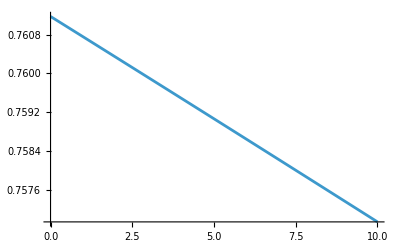

```mathematica
Plot[v[x],{x,0,10}]
```

```mathematica
y[x_]:=A*(-Exp[x/r]+c)^2
y[x]
```

(10-ⅇ^x)^2

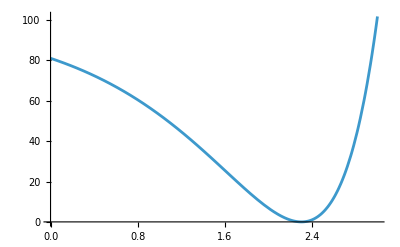

```mathematica
Plot[y[x],{x,0,3}]
```